```mathematica
LegendreP[3,x]
```

1/2 (-3 x+5 x^3)

```mathematica
K[n_, x_] :=Sqrt[n+1/2] LegendreP[n,x]
```

```mathematica
K[3, x]
```

(√7 (-3 π^2 x+5 x^3))/(2 π^3)

```mathematica
Integrate[K[i, x]K[j, x],{x,-Pi,Pi}]
```

∫_-π^π √(1+2 i) √(1+2 j) LegendreP[i,x/π] LegendreP[j,x/π]ⅆx

```mathematica
Integrate[LegendreP[i, x]LegendreP[j, x],{x,-1,1}]
```

∫_-1^1 LegendreP[i,x] LegendreP[j,x]ⅆx

```mathematica
MatrixForm[Table[Integrate[LegendreP[i, x]LegendreP[j, x],{x,-1,1}],{i,0,5},{j,0,5}]]
```

(2 | 0 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | 0 | 0
0 | 0 | 2/5 | 0 | 0 | 0
0 | 0 | 0 | 2/7 | 0 | 0
0 | 0 | 0 | 0 | 2/9 | 0
0 | 0 | 0 | 0 | 0 | 2/11)

```mathematica
MatrixForm[Table[Integrate[K[i, x]K[j, x],{x,-1,1}],{i,0,5},{j,0,5}]]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
K[n_, x_] :=Sqrt[(2n+1)/(2Pi)] LegendreP[n,x/Pi]
```

```mathematica
MatrixForm[Table[Integrate[K[i, x]K[j, x],{x,-Pi,Pi}],{i,0,5},{j,0,5}]]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
LegendreP1[n_, x_]:=Sqrt[(2n+1)/(2Pi)] LegendreP[n,x/Pi]
```

```mathematica
?LegendreP1
```

Global`LegendreP1

LegendreP1[n_,x_]:=√((2 n+1)/(2 π)) LegendreP[n,x/π]

```mathematica
MatrixForm[Table[Integrate[LegendreP1[i, x]LegendreP1[j, x],{x,-Pi,Pi}],{i,0,5},{j,0,5}]]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
LegendreP2[n_, x_]:=Sqrt[(2n+1)/2] LegendreP[n,x]
```

```mathematica
MatrixForm[Table[Integrate[LegendreP2[i, x]LegendreP2[j, x],{x,-1,1}],{i,0,5},{j,0,5}]]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
GeneratingFunction[LegendreP[n,x],n,t]
```

1/(√(1+t^2-2 t x))

```mathematica
D[GeneratingFunction[LegendreP[n,x],n,t], t]
```

-(2 t-2 x)/(2 (1+t^2-2 t x)^(3/2))

```mathematica
LegendreP3[0, x_] := 1
LegendreP3[1, x_] := x
LegendreP3[n_, x_] := (2(n-1)+1)/n x LegendreP3[n-1, x]-(n-1)/n LegendreP3[n-2, x]
```

```mathematica
LegendreP3[3, x]
```

```mathematica
Simplify[LegendreP3[3,x]]
```

1/2 x (-3+5 x^2)

```mathematica
LegendreP3[1,x]
```

x

```mathematica
LegendreP[3, x]
```

1/2 (-3 x+5 x^3)

```mathematica
√(2(n+1)+1)
```

```mathematica
?LegendreP3
```

Global`LegendreP3

LegendreP3[0,x_]:=1
 
LegendreP3[1,x_]:=x
 
LegendreP3[n_,x_]:=((2 (n-1)+1) x LegendreP3[n-1,x])/n-((n-1) LegendreP3[n-2,x])/n

```mathematica
Clear[LegendreP3]
```

```mathematica
(2(n-1)+1)/n
```

(1+2 (-1+n))/n

```mathematica
Simplify[(1+2 (-1+n))/n]
```

2-1/n

```mathematica
√(2n+1) (2(n-1)+1)/n
```

((1+2 (-1+n)) √(1+2 n))/n

```mathematica
Simplify[%]
```

((-1+2 n) √(1+2 n))/n

```mathematica
√(2n+1)(n-1)/n
```

((-1+n) √(1+2 n))/n

```mathematica
Simplify[%]
```

((-1+n) √(1+2 n))/n

```mathematica
LegendreP4[0, x_] := 1
LegendreP4[1, x_] := x
LegendreP4[n_, x_] := n/(√(4n^2-1))x LegendreP3[n-1, x]-(n-1)/(√(4(n-1)^2-1))LegendreP3[n-2, x]
```

```mathematica
?LegendreP4
```

Global`LegendreP4

LegendreP4[0,x_]:=1
 
LegendreP4[1,x_]:=x
 
LegendreP4[n_,x_]:=(n x LegendreP3[n-1,x])/(√(4 n^2-1))-((n-1) LegendreP3[n-2,x])/(√(4 (n-1)^2-1))

```mathematica
MatrixForm[Table[Integrate[LegendreP4[i, x]LegendreP4[j, x],{x,-1,1}],{i,0,5},{j,0,5}]]
```

(2 | 0 | -2/(√3)+4/(3 √15) | 0 | 0 | 0
0 | 2/3 | 0 | -4/(3 √15)+4/(5 √35) | 0 | 0
-2/(√3)+4/(3 √15) | 0 | 58/75-8/(9 √5) | 0 | (8 √(5/21))/21-(6 √(3/7))/25+2/(5 √21)-8/(5 √105) | 0
0 | -4/(3 √15)+4/(5 √35) | 0 | 2554/11025-(12 √(3/7))/25+4/(5 √21) | 0 | (5 √(35/11))/24+18/(35 √5)-(6 √5)/49-(3 √(55/7))/14+39/(8 √385)
0 | 0 | (8 √(5/21))/21-(6 √(3/7))/25+2/(5 √21)-8/(5 √105) | 0 | (2 (6943-1944 √5))/99225 | 0
0 | 0 | 0 | (5 √(35/11))/24+18/(35 √5)-(6 √5)/49-(3 √(55/7))/14+39/(8 √385) | 0 | 16166/160083-(260 √(7/11))/81+460/(21 √77))

```mathematica
cf[-1]:=0
cf[n_]:= (π(n+1))/(√(4(n+1)^2-1))
```

```mathematica
P[0,w_]=1; 
P[1,w_]:=w/cf[0];
P[deg_,w_]:=P[deg,w]=w/cf[deg-1] P[deg-1,w]-cf[deg-2]/cf[deg-1] P[deg-2,w];
```

```mathematica
P[3,x]
```

-(2 √7 x)/(3 π)+(√35 x (-(√5)/2+(3 √5 x^2)/(2 π^2)))/(3 π)

```mathematica
cf[n-1]
```

(n π)/(√(-1+4 n^2))

```mathematica
cf[n-2]/cf[n-1]
```

```mathematica
Simplify[((-1+n) √(-1+4 n^2))/(√(-1+4 (-1+n)^2) n)]
```

((-1+n) √(-1+4 n^2))/(n √(3-8 n+4 n^2))

```mathematica
LegendreP5[0, x_] := 1
LegendreP5[1, x_] := x/cf[0]
LegendreP5[n_, x_] := LegendreP5[n, x]=x/cf[n-1] LegendreP3[n-1, x]-cf[n-2]/cf[n-1] LegendreP3[n-2, x]
```

```mathematica
MatrixForm[Table[Integrate[LegendreP5[i, x]LegendreP5[j, x],{x,-Pi,Pi}],{i,0,5},{j,0,5}]]
```

(2 π | 0 | -√5 π+√(5/3) π^2 | 0 | (9 π)/(4 √5)-(3 √7 π^2)/4-(9 π^3)/(4 √5)+(3 √7 π^4)/4 | 0
0 | 2 π | 0 | -1/3 √(35/3) π-(4 √7 π^2)/9+√(21/5) π^3 | 0 | (3 √33 π)/20+4/5 √(33/7) π^2-(9 √33 π^3)/10-4/5 √(33/7) π^4+(3 √33 π^5)/4
-√5 π+√(5/3) π^2 | 0 | (5 π)/2-(5 π^2)/(√3)+(3 π^3)/2 | 0 | -(9 π)/8+(3 √3 π^2)/8+(3 √35 π^2)/8+(9 π^3)/8-9/8 √(21/5) π^3-(27 √3 π^4)/40-(3 √35 π^4)/8+15/8 √(15/7) π^5 | 0
0 | -1/3 √(35/3) π-(4 √7 π^2)/9+√(21/5) π^3 | 0 | 1/810 π (525-1330 π^2+2025 π^4+56 √15 π (5-9 π^2)) | 0 | -1/8 √(77/5) π-2/3 √(11/5) π^2-1/10 √(77/3) π^2-8/15 √(11/3) π^3+39/40 √(77/5) π^3+28/15 √(11/5) π^4+(√231 π^4)/5+8/15 √(11/3) π^5-25/8 √(55/7) π^5-1/2 √(77/3) π^6-(2 √55 π^6)/7+(7 √385 π^7)/24
(9 π)/(4 √5)-(3 √7 π^2)/4-(9 π^3)/(4 √5)+(3 √7 π^4)/4 | 0 | -(9 π)/8+(3 √3 π^2)/8+(3 √35 π^2)/8+(9 π^3)/8-9/8 √(21/5) π^3-(27 √3 π^4)/40-(3 √35 π^4)/8+15/8 √(15/7) π^5 | 0 | (π (2835-1890 √35 π+14175 π^2+5292 √35 π^3-42147 π^4-4050 √35 π^5+30625 π^6))/5600 | 0
0 | (3 √33 π)/20+4/5 √(33/7) π^2-(9 √33 π^3)/10-4/5 √(33/7) π^4+(3 √33 π^5)/4 | 0 | -1/8 √(77/5) π-2/3 √(11/5) π^2-1/10 √(77/3) π^2-8/15 √(11/3) π^3+39/40 √(77/5) π^3+28/15 √(11/5) π^4+(√231 π^4)/5+8/15 √(11/3) π^5-25/8 √(55/7) π^5-1/2 √(77/3) π^6-(2 √55 π^6)/7+(7 √385 π^7)/24 | 0 | (π (43659+66528 √7 π-346500 π^2-465696 √7 π^3+1952874 π^4+807840 √7 π^5-3184500 π^6-431200 √7 π^7+1620675 π^8))/117600)

```mathematica
?LegendreP5
```

Global`LegendreP5

LegendreP5[2,x]=-(√5)/2+(√15 x^2)/(2 π)
 
LegendreP5[3,x]=-2/3 √(7/3) x+(√35 x (-1/2+(3 x^2)/2))/(3 π)
 
LegendreP5[4,x]=-(9 (-1/2+(3 x^2)/2))/(4 √5)+(3 √7 x (-(2 x)/3+5/3 x (-1/2+(3 x^2)/2)))/(4 π)
 
LegendreP5[5,x]=-4/5 √(11/7) (-(2 x)/3+5/3 x (-1/2+(3 x^2)/2))+(3 √11 x (-3/4 (-1/2+(3 x^2)/2)+7/4 x (-(2 x)/3+5/3 x (-1/2+(3 x^2)/2))))/(5 π)
 
LegendreP5[0,x_]:=1
 
LegendreP5[1,x_]:=x/cf[0]
 
LegendreP5[n_,x_]:=LegendreP5[n,x]=(x LegendreP3[n-1,x])/cf[n-1]-(cf[n-2] LegendreP3[n-2,x])/cf[n-1]

```mathematica
MatrixForm[Table[Integrate[P[i, x]P[j, x],{x,-Pi,Pi}],{i,0,5},{j,0,5}]]
```

(2 π | 0 | 0 | 0 | 0 | 0
0 | 2 π | 0 | 0 | 0 | 0
0 | 0 | 2 π | 0 | 0 | 0
0 | 0 | 0 | 2 π | 0 | 0
0 | 0 | 0 | 0 | 2 π | 0
0 | 0 | 0 | 0 | 0 | 2 π)

```mathematica
LegendreP5[3,x]
```

-2/3 √(7/3) x+(√35 x (-1/2+(3 x^2)/2))/(3 π)

```mathematica
Simplify[-2/3 √(7/3) x+(√35 x (-1/2+(3 x^2)/2))/(3 π)]
```

-2/3 √(7/3) x+(√35 x (-1+3 x^2))/(6 π)

```mathematica
Simplify[P[3,x]]
```

(√7 x (-3 π^2+5 x^2))/(2 π^3)

```mathematica
?P
```

Global`P

P[2,x]=-(√5)/2+(3 √5 x^2)/(2 π^2)
 
P[3,x]=-(2 √7 x)/(3 π)+(√35 x (-(√5)/2+(3 √5 x^2)/(2 π^2)))/(3 π)
 
P[4,x]=-(9 (-(√5)/2+(3 √5 x^2)/(2 π^2)))/(4 √5)+(3 √7 x (-(2 √7 x)/(3 π)+(√35 x (-(√5)/2+(3 √5 x^2)/(2 π^2)))/(3 π)))/(4 π)
 
P[5,x]=-4/5 √(11/7) (-(2 √7 x)/(3 π)+(√35 x (-(√5)/2+(3 √5 x^2)/(2 π^2)))/(3 π))+(3 √11 x (-(9 (-(√5)/2+(3 √5 x^2)/(2 π^2)))/(4 √5)+(3 √7 x (-(2 √7 x)/(3 π)+(√35 x (-(√5)/2+(3 √5 x^2)/(2 π^2)))/(3 π)))/(4 π)))/(5 π)
 
P[0,w_]=1
 
P[1,w_]:=w/cf[0]
 
P[deg_,w_]:=P[deg,w]=(w P[deg-1,w])/cf[deg-1]-(cf[deg-2] P[deg-2,w])/cf[deg-1]

```mathematica
Clear[P, cf]
```

```mathematica
?P
```

Global`P

```mathematica
cf[-1]:=0
cf[n_]:= (π(n+1))/(√(4(n+1)^2-1))
```

```mathematica
P[0,w_]=1; 
P[1,w_]:=w/cf[0];
P[deg_,w_]:=P[deg,w]=w/cf[deg-1] P[deg-1,w]-cf[deg-2]/cf[deg-1] P[deg-2,w];
```

```mathematica
Clear[Leg]
Leg[0,x_]:=1
Leg[1,x_]:=x/(1/(√3))
Leg[n_,x_]:=Leg[n,x]=x/(n/(√(-1+4 n^2)))Leg[n-1,x]-((-1+n) √(-1+4 n^2))/(√(-1+4 (-1+n)^2) n)Leg[n-2,x]
```

```mathematica
x/(n/(√(-1+4 n^2)))
```

(√(-1+4 n^2) x)/n

```mathematica
MatrixForm[Table[Integrate[Leg[i, x]Leg[j, x],{x,-1,1}],{i,0,5},{j,0,5}]]
```

(2 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2)

```mathematica
?Leg
```

Global`Leg

Leg[2,x]=-(√5)/2+(3 √5 x^2)/(2 π^2)
 
Leg[3,x]=-(2 √7 x)/(3 π)+(√35 x (-(√5)/2+(3 √5 x^2)/(2 π^2)))/(3 π)
 
Leg[4,x]=-(9 (-(√5)/2+(3 √5 x^2)/(2 π^2)))/(4 √5)+(3 √7 x (-(2 √7 x)/(3 π)+(√35 x (-(√5)/2+(3 √5 x^2)/(2 π^2)))/(3 π)))/(4 π)
 
Leg[5,x]=-4/5 √(11/7) (-(2 √7 x)/(3 π)+(√35 x (-(√5)/2+(3 √5 x^2)/(2 π^2)))/(3 π))+(3 √11 x (-(9 (-(√5)/2+(3 √5 x^2)/(2 π^2)))/(4 √5)+(3 √7 x (-(2 √7 x)/(3 π)+(√35 x (-(√5)/2+(3 √5 x^2)/(2 π^2)))/(3 π)))/(4 π)))/(5 π)
 
Leg[0,x_]:=1
 
Leg[1,x_]:=x/(π/(√3))
 
Leg[n_,x_]:=Leg[n,x]=(x Leg[n-1,x])/((n π)/(√(-1+4 n^2)))-(((-1+n) √(-1+4 n^2)) Leg[n-2,x])/(√(-1+4 (-1+n)^2) n)

```mathematica
cf[0]
```

π/(√3)

```mathematica
cf[n-1]
```

(n π)/(√(-1+4 n^2))

```mathematica
cf[n-2]/cf[n-1]
```

((-1+n) √(-1+4 n^2))/(√(-1+4 (-1+n)^2) n)

```mathematica
Clear[Q]
Q[0, x_]:=1
Q[1, x_]:=√3 x
Q[n_, x_]:=Q[n,x]=(√(4 n^2-1))/n x Q[n-1, x]-((n-1)√(4 n^2-1))/(n √(4(n-1)^2-1)) Q[n-2, x]
```

```mathematica
MatrixForm[Table[Integrate[Q[i, x]Q[j, x],{x,-1,1}],{i,0,5},{j,0,5}]]
```

(2 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2)

```mathematica
Simplify[(n √(4(n+1)^2-1))/((n+1)√(4 n^2-1))]
```

(n √(3+8 n+4 n^2))/((1+n) √(-1+4 n^2))

```mathematica
Clear[c]
c[n_]:=(√(4 n^2-1))/n
```

```mathematica
Clear[Q]
Q[0, x_]:=1
Q[1, x_]:=c[1]x
Q[n_, x_]:=Q[n,x]=x c[n] Q[n-1, x]-c[n]/c[n-1] Q[n-2, x]
```

```mathematica
MatrixForm[Table[Integrate[Q[i, x]Q[j, x],{x,-1,1}],{i,0,5},{j,0,5}]]
```

(2 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2)

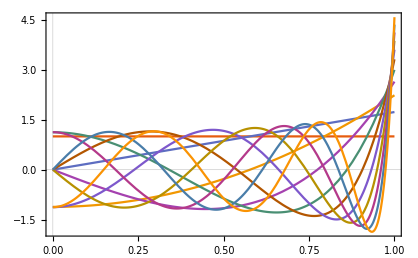

```mathematica
Plot[Evaluate[Table[Q[i,x],{i,0, 10}]],{x, 0, 1},PlotTheme->"Scientific",ImageSize->{418,258},AspectRatio->Full]
```

```mathematica
Export["/Users/tiao/Dropbox/UNSW/honours-thesis/figures/legendre_normalized.pdf",%261,"PDF"]
```

/Users/tiao/Dropbox/UNSW/honours-thesis/figures/legendre_normalized.pdf

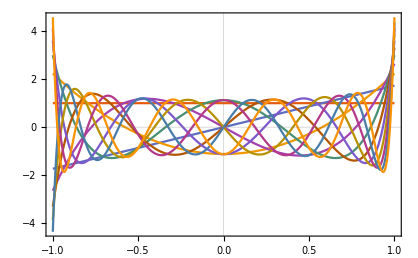

```mathematica
Plot[Evaluate[Table[Q[i,x],{i,0, 10}]],{x, -1, 1},PlotTheme->"Scientific",ImageSize->{418,258},AspectRatio->Full]
```

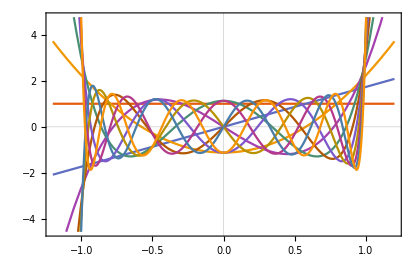

```mathematica
Plot[Evaluate[Table[Q[i,x],{i,0, 10}]],{x, -1.2, 1.2},PlotTheme->"Scientific",ImageSize->{418,258},AspectRatio->Full]
```

```mathematica
K[n_,t_]:=
```

```mathematica
Clear[K]
K[n_, t_]:=Q[n, D[#,t]]&
```

```mathematica
?K
```

K is a default generic name for a summation index in a symbolic sum.

```mathematica
K[3, t][4 t^3]
```

-8 √7 t^2+4 √35 t^2 (-(√5)/2+216 √5 t^4)

```mathematica
?K
```

K is a default generic name for a summation index in a symbolic sum.

```mathematica
Clear[K]
?D
```

D[f,x] gives the partial derivative ∂f/∂x. 
D[f,{x,n}] gives the multiple derivative ∂^n f/∂x^n. 
D[f,x,y,…] differentiates f successively with respect to x,y,….
D[f,{{x_1,x_2,…}}] for a scalar f gives the vector derivative (∂f/∂x_1,∂f/∂x_2,…). 
D[f,{array}] gives a tensor derivative.

```mathematica
K[f_,{x_, n_}] := (-ⅈ)^n Q[n, ⅈ D[f, x]]
```

```mathematica
K[4 t^3,{t, 3}]
```

-8 √7 t^2+4 √35 t^2 (-(√5)/2+216 √5 t^4)